# Лабораторная работа 2.

Шпак Андрей, 3 курс, 5 группа.

## Задание 1. Гармонические колебания.

### Задание 1.1 (Амплитуда колебаний)

m - масса физического тела, r(t) - координата тела вдоль оси пружины. r = 0 положение равновесия, r(t) > 0, когда пружина растянута. r(t) < 0, когда она сжата. L - расстояние между положением равновесия и стенкой.

```mathematica
ClearAll[r0,v0,L,ω];
```

```mathematica
sol=DSolveValue[{r''[t]+ω^2*r[t]==0,r[0]==r0,r'[0]==v0},r[t],t]
```

(r0 ω Cos[t ω]+v0 Sin[t ω])/ω

### Задание 1.2 (Динамическая визуализация с учетом соударения тела о стенку)

```mathematica
Manipulate[Animate[Graphics[{Red,Line[{{0,0},{L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]],0}}],Black,PointSize@0.03,Point[{L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]],0}],Line[{{0,-100},{0,100}}]},PlotRange->{{-10,10},{-10,10}}],{t,0,10},AnimationRunning->(L+Sqrt[r0^2+v0^2/ω^2]*Cos[ω*t+ArcTan[-v0/(ω*r0)]]>0)],{r0,1,10},{v0,0,10},{ω,1,10},{L,1,10}]
```

## Задание 2. Колебания с учетом сопротивления среды.

### Задание 2.2 (Качественный анализ по теореме Ляпунова)

Мне было сначала удобно сделать этот пункт, так как тут я вывел важное значение, которое буду потом сравнивать с μ. Это будет Sqrt(μ^2-4km). И дальше уже я буду смотреть, какие случаи возникают при разных μ.

Нужно ввести замену, как в механике, что и очевидно: v= dr/dt. Тогда уравнения примет вид m*v’[t] == -k*r[t] - μ*v. Нужно разделить на m обе части.

```mathematica
ClearAll[r0,v0,L,ω];
```

```mathematica
DSolveValue[{m*r''[t]==-k*r[t]-μ*r'[t],r[0]==r0,r'[0]==v0},r[t],t]
```

1/(2 √(-4 k m+μ^2))(-2 ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) m v0+2 ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) m v0-ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) r0 μ+ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) r0 μ+ⅇ^(1/2 t (-μ/m-(√(-4 k m+μ^2))/m)) r0 √(-4 k m+μ^2)+ⅇ^(1/2 t (-μ/m+(√(-4 k m+μ^2))/m)) r0 √(-4 k m+μ^2))

### Задание 2.1 (Качественный анализ по фазовому портрету)

Для получения каких-либо результатов, я буду сравнивать μ и значение 4k*m, вывод которого я получил из записей выше. Так как константа 4m постоянная величина, то фактически сравнение идет между μ и k. 
	Затухающие колебания - коэффициент вязкого трения меньше значения 4k*m. Устойчивый фокус.

```mathematica
k=1;
m=1;
μ=1;
```

```mathematica
μ^2-4k*m
```

-3

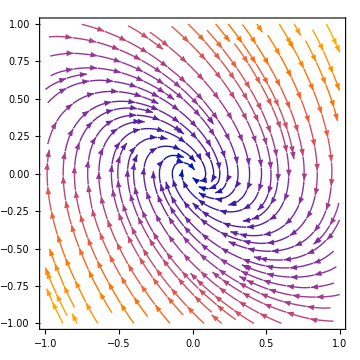

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Критические колебания, коэффициент вязкого трения равен значению 4 k*m. Это будет устойчивый узел.

```mathematica
μ=Sqrt[4k*m];
```

```mathematica
μ^2-4k*m
```

0

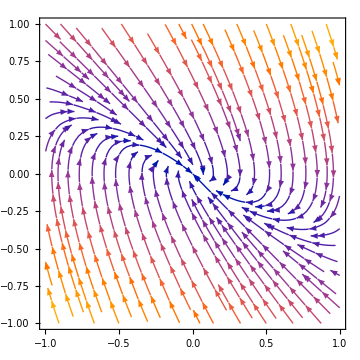

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Апериодическое затухание. Коэффициент вязкого трения больше, чем значение 4 k*m - устойчивый узел.

```mathematica
μ=5;
```

```mathematica
μ^2-4k*m
```

21

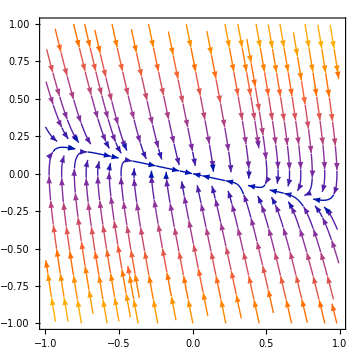

```mathematica
StreamPlot[{v,-k/m*r-μ/m*v},{r,-1,1},{v,-1,1}]
```

Выводы согласуются с аналитическим решением на листике.

### Задание 2.3 (Анализ частных случаев)

Частные случаи. Сравним μ^2 и 4 ω^2 m:

```mathematica
k=0.001;
m=1;
μ=1.82*10^-5;
```

```mathematica
μ^2-4k*m
```

-0.004

```mathematica
μ=1.002*10^-3;
```

```mathematica
μ^2-4k*m
```

-0.003999

```mathematica
μ=1.49;
```

```mathematica
μ^2-4k*m
```

2.2161

В первых двух случаях получены отрицательные значения и значит решения характерестического уравнения будут комплексными с отрицательной действительной частью, что свидетельствует о затухающий колебаниях. Второй случай будет соответствовать апериодическому затуханию. Под корнем получаем положительное число и корни будут действительные, но все так же отрицательные.

## Задание 3. Вынужденные колебания.

### Задание 3.1 (Частное решение математической модели)

Наличие резонанса.

Не резонансный случай.

### Задание 3.2 (Графики вынужденных колебаний)

Наличие резонанса.

```mathematica
r0=1;
v0=5;
ω=10;
m=1;
Subscript[F, 0]=5;
Subscript[ω, 2]=2;
k=3;
```

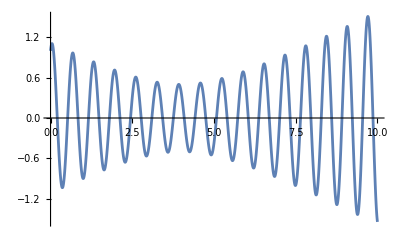

```mathematica
Plot[(r0*ω*Cos[t*ω]+v0*Sin[t*ω])/ω+(-t*Subscript[F, 0])/(2ω*m)*Cos[ω*t],{t,0,10}]
```

Не резонансный случай.

```mathematica
r0=1;
v0=1;
ω=2;
m=2;
Subscript[F, 0]=5;
Subscript[ω, 2]=5;
k=6;
```

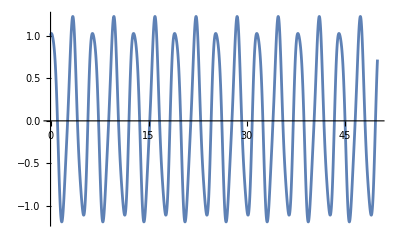

```mathematica
Plot[(r0*ω*Cos[t*ω]+v0*Sin[t*ω])/ω+Subscript[F, 0]/(k-m*Subscript[ω, 2]^2)*Sin[Subscript[ω, 2]*t],{t,0,50}]
```

## Задание 4. Система химических реакций двух веществ.

X - вещество, которое поступает в систему с постоянной скоростью k_1=const>0, превращается в вещество Y со скоростью, пропорциональной концентрации вещества X и коэффициентом пропорциональности k_2=const>0. Вещество Y выводится из системы со скоростью, пропорциональной концентрации вещества Y, и коэффициентом пропорциональности k_3=const>0. x(0) = x_0, y(0)=y_0,

```mathematica
X'[t]=Subscript[k, 1]-Subscript[k, 2]*X[t]
Y'[t]=Subscript[k, 2]*X[t]-Subscript[k, 3]*Y[t]
```

```mathematica
k1=1;
k2=2;
k3=3;
```

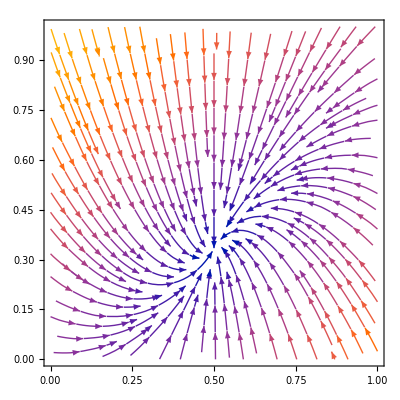

```mathematica
StreamPlot[{k1-k2 x,k2 x-k3 y},{x,0,1},{y,0,1}]
```

Дальше надо показать, что корни отрицательные.